### 1. Matrix基础

```mathematica
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[i^2, {i, 1, 10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Array[#^2 + #2 &,{3,3}]
```

{{2,3,4},{5,6,7},{10,11,12}}

```mathematica
MatrixForm[HilbertMatrix[3]]
```

(1 | 1/2 | 1/3
1/2 | 1/3 | 1/4
1/3 | 1/4 | 1/5)

```mathematica
MatrixForm[ConstantArray[m,{3,4}]]
```

(m | m | m | m
m | m | m | m
m | m | m | m)

```mathematica
m = 1
```

1

```mathematica
MatrixForm[]
```

(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)

```mathematica
MatrixForm[SparseArray[{{2,2}->1,{7,1}->2}]]
```

(0 | 0
0 | 1
0 | 0
0 | 0
0 | 0
0 | 0
2 | 0)

```mathematica
Normal[%]
```

{{0,0},{0,1},{0,0},{0,0},{0,0},{0,0},{2,0}}

### 2. Playground

```mathematica
AngleVector[θ]
```

{Cos[θ],Sin[θ]}

```mathematica
AngleVector[Pi/6]
```

{(√3)/2,1/2}

```mathematica
V1 = {{1},{2}}
V1 * AngleVector[Pi/6]
AngleVector[Pi/6] * V1
V2 = {1, 2}
V2 * AngleVector[Pi/6]
AngleVector[Pi/6] * V2
```

{{1},{2}}

{{(√3)/2},{1}}

{{(√3)/2},{1}}

{1,2}

{(√3)/2,1}

{(√3)/2,1}

```mathematica
A = {{x, xy},{x+y,y}}
```

{{x,xy},{x+y,y}}

```mathematica
MatrixForm[A]
```

(x | xy
x+y | y)

```mathematica
B = {{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
Solve[A == B, {x, y}]
```

{}

```mathematica
Solve[A ~ B, x]
```

{}

```mathematica
Solve[x^2+ax+1==0,x]
```

{{x→-√(-1-ax)},{x→√(-1-ax)}}

```mathematica
Solve[ax^2+bx+c==0,x]
```

{}

```mathematica
LinearSolve[A, B]
```

{{(3 xy-y)/(x xy-x y+xy y),(2 (2 xy-y))/(x xy-x y+xy y)},{(2 x-y)/(-x xy+x y-xy y),(2 (x-y))/(-x xy+x y-xy y)}}

```mathematica
Length[A]
```

2

```mathematica
c = {RandomReal[{1,100}, 3],RandomReal[{1,100},3],RandomReal[{1,100},3]}
```

{{68.4485,83.2149,37.9183},{44.7389,76.0031,39.5774},{32.3764,98.7525,17.3035}}

```mathematica
MatrixForm[c]
```

(68.4485 | 83.2149 | 37.9183
44.7389 | 76.0031 | 39.5774
32.3764 | 98.7525 | 17.3035)

```mathematica
Transpose[c]
```

{{68.4485,44.7389,32.3764},{83.2149,76.0031,98.7525},{37.9183,39.5774,17.3035}}

```mathematica
LUDecomposition[c]
```

{{{68.4485,83.2149,37.9183},{0.473004,59.3915,-0.631981},{0.653614,0.363901,15.0234}},{1,3,2},23.2872}

```mathematica
Det[c]
```

-61073.9

```mathematica
c[[1]]
```

{68.4485,83.2149,37.9183}

```mathematica
Length[c]
```

3

```mathematica
c[[2;;3]]
```

{{44.7389,76.0031,39.5774},{32.3764,98.7525,17.3035}}

```mathematica
c[[2]]=RandomReal[{1,200},3]
```

{163.218,95.6946,96.2537}

```mathematica
MatrixForm[c]
```

(68.4485 | 83.2149 | 37.9183
163.218 | 95.6946 | 96.2537
32.3764 | 98.7525 | 17.3035)

```mathematica
VectorQ[c]
```

False

```mathematica
VectorQ[c[2]]
```

False

```mathematica
d = {RandomReal[{1,10}], RandomReal[{1,10}],RandomReal[{1,10}]}
```

{4.25078,9.61632,8.06545}

```mathematica
c.d
```

c.d

```mathematica
d={1,2,3}
```

{1,2,3}

```mathematica
c.d
```

c.d

```mathematica
v1 = {1,2,3};
v2 = {4,5,6};
Dot[v1, v2]
```

32

```mathematica
Cross[v1,v2]
```

{-3,6,-3}

```mathematica
Norm[v1]
```

√14

```mathematica
Normalize[v1]
```

{1/(√14),√(2/7),3/(√14)}

```mathematica
Total[v1]
```

6

```mathematica
Length[v1]
```

3

```mathematica
Div[{f[x,y,z],g[x,y,z],h[x,y,z]},{x,y,z}]
```

h^(0,0,1)[x,y,z]+g^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]

```mathematica
(*∇_{x,y,z} \[Application]{y,-x,z}*)
∇_{x,y,z} .{y,-x,z}
```

1

```mathematica
Curl[{f[x,y,z],g[x,y,z],h[x,y,z]},{x,y,z}]
```

{-g^(0,0,1)[x,y,z]+h^(0,1,0)[x,y,z],f^(0,0,1)[x,y,z]-h^(1,0,0)[x,y,z],-f^(0,1,0)[x,y,z]+g^(1,0,0)[x,y,z]}

```mathematica
Curl[{y,-x},{x,y}]
```

-2

```mathematica
∇_{x,y,z} × {y,-x,z}
```

{0,0,-2}

```mathematica
VectorAngle[{1,0},{1,1}]
```

π/4

```mathematica
Degree[Dot[Normalize[{1,0}],Normalize[{1,1}]]]
```

°[1/(√2)]

```mathematica
Clear[{a,b,c,x,y,z}]
{a,b,c} . {x,y,z}
```

a x+b y+c z

```mathematica
Projection[{5,6,7},{1,0,0}]
```

{5,0,0}

```mathematica
Orthogonalize[{{1,0,1},{1,1,1}}]
```

{{1/(√2),0,1/(√2)},{0,1,0}}

```mathematica
av = Array[Subscript[a, ##]&,{2}];
bv = Array[Subscript[b, ##]&,{2}];
KroneckerProduct[av, bv]  // MatrixForm
```

(a_1 b_1 | a_1 b_2
a_2 b_1 | a_2 b_2)

```mathematica
a = {{1},{2},{3}};
b = {4,5,6};
```

```mathematica
Row[a]
```

{1}{2}{3}

```mathematica
Column[a]
```

{1}
{2}
{3}

```mathematica
Column[b]
```

4
5
6

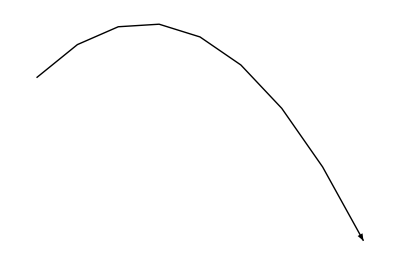
{-Graphics-,-Graphics3D-}

```mathematica
{Graphics[{Arrow[BezierCurve[{{0,0},{1,1},{2,-1}}]]}],
Graphics3D[{Arrow[BSplineCurve[{{0,0,0},{1,1,1},{2,-1,1},{3,0,2}}]]}]}
```

```mathematica
RandomReal[{1, 100}, 10]
```

{28.7421,31.2737,2.13801,52.5869,33.3834,3.37454,87.9475,35.8073,97.2195,77.3855}

```mathematica
a = Array[RandomReal[{0, 1}]&,{3,3}]
a // MatrixForm
```

{{0.53088,0.361702,0.926787},{0.984272,0.893606,0.893206},{0.495111,0.956627,0.250888}}

(0.53088 | 0.361702 | 0.926787
0.984272 | 0.893606 | 0.893206
0.495111 | 0.956627 | 0.250888)

```mathematica
i = IdentityMatrix[3] 
i // MatrixForm
```

{{1,0,0},{0,1,0},{0,0,1}}

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
b = (i - a)
b // MatrixForm
```

{{0.46912,-0.361702,-0.926787},{-0.984272,0.106394,-0.893206},{-0.495111,-0.956627,0.749112}}

(0.46912 | -0.361702 | -0.926787
-0.984272 | 0.106394 | -0.893206
-0.495111 | -0.956627 | 0.749112)

```mathematica
(a +b) // MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

### 3. 美国1958国民经济数据练习

```mathematica
c1958 = {{0.1588,0.0064,0.0025,0.0304,0.0014,0.0083,0.1594},{0.0057,0.2645,0.0436,0.0099,0.0083,0.0201,0.3413},{0.0264,0.1506,0.3557,0.0139,0.0142,0.0070,0.0236},{0.3299,0.0565,0.0495,0.3636,0.0204,0.0483,0.0649},{0.0089,0.0081,0.0333,0.0295,0.3412,0.0237,0.0020},{0.1190,0.0901,0.0996,0.1260,0.1722,0.2368,0.3369},{0.0063,0.0126,0.0196,0.0098,0.0064,0.0132,0.0012}}
c1958 // MatrixForm
```

{{0.1588,0.0064,0.0025,0.0304,0.0014,0.0083,0.1594},{0.0057,0.2645,0.0436,0.0099,0.0083,0.0201,0.3413},{0.0264,0.1506,0.3557,0.0139,0.0142,0.007,0.0236},{0.3299,0.0565,0.0495,0.3636,0.0204,0.0483,0.0649},{0.0089,0.0081,0.0333,0.0295,0.3412,0.0237,0.002},{0.119,0.0901,0.0996,0.126,0.1722,0.2368,0.3369},{0.0063,0.0126,0.0196,0.0098,0.0064,0.0132,0.0012}}

(0.1588 | 0.0064 | 0.0025 | 0.0304 | 0.0014 | 0.0083 | 0.1594
0.0057 | 0.2645 | 0.0436 | 0.0099 | 0.0083 | 0.0201 | 0.3413
0.0264 | 0.1506 | 0.3557 | 0.0139 | 0.0142 | 0.007 | 0.0236
0.3299 | 0.0565 | 0.0495 | 0.3636 | 0.0204 | 0.0483 | 0.0649
0.0089 | 0.0081 | 0.0333 | 0.0295 | 0.3412 | 0.0237 | 0.002
0.119 | 0.0901 | 0.0996 | 0.126 | 0.1722 | 0.2368 | 0.3369
0.0063 | 0.0126 | 0.0196 | 0.0098 | 0.0064 | 0.0132 | 0.0012)

```mathematica
d1958 = {74000,56000,10500,25000,17500,196000,5000}
d1958 // MatrixForm
```

{74000,56000,10500,25000,17500,196000,5000}

(74000
56000
10500
25000
17500
196000
5000)

```mathematica
i1958 = IdentityMatrix[Length[c1958]]
i1958 // MatrixForm
```

{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1}}

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
inv1958 = Inverse[i1958 - c1958]
inv1958 // MatrixForm
```

{{1.22119,0.0270856,0.0225685,0.0677001,0.0135465,0.0226551,0.216748},{0.0432427,1.40455,0.124385,0.0465836,0.0403637,0.0516298,0.510313},{0.0805574,0.338749,1.59274,0.0555055,0.0507739,0.0326252,0.180957},{0.673244,0.190455,0.176277,1.64481,0.094835,0.126639,0.326472},{0.0635781,0.0531293,0.100977,0.0897173,1.53928,0.057515,0.0589992},{0.340947,0.271065,0.295271,0.325295,0.384174,1.36736,0.637139},{0.0213481,0.0303284,0.0392457,0.0231163,0.0174619,0.0211164,1.02456}}

(1.22119 | 0.0270856 | 0.0225685 | 0.0677001 | 0.0135465 | 0.0226551 | 0.216748
0.0432427 | 1.40455 | 0.124385 | 0.0465836 | 0.0403637 | 0.0516298 | 0.510313
0.0805574 | 0.338749 | 1.59274 | 0.0555055 | 0.0507739 | 0.0326252 | 0.180957
0.673244 | 0.190455 | 0.176277 | 1.64481 | 0.094835 | 0.126639 | 0.326472
0.0635781 | 0.0531293 | 0.100977 | 0.0897173 | 1.53928 | 0.057515 | 0.0589992
0.340947 | 0.271065 | 0.295271 | 0.325295 | 0.384174 | 1.36736 | 0.637139
0.0213481 | 0.0303284 | 0.0392457 | 0.0231163 | 0.0174619 | 0.0211164 | 1.02456)

```mathematica
(inv1958 . (i1958 - c1958)) // MatrixForm
Dot[inv1958, (i1958 - c1958)] // MatrixForm
varify1958 =(inv1958 . (i1958 - c1958))
Clear[{a,b,c,d}]
{{a,b},{c,d}}.{{1,2},{3,4}} // MatrixForm
```

(1. | 3.03577×10^-18 | 1.73472×10^-18 | -1.73472×10^-17 | -6.50521×10^-19 | 0. | 2.77556×10^-17
-4.33681×10^-19 | 1. | 1.38778×10^-17 | -2.60209×10^-18 | -2.1684×10^-18 | 5.20417×10^-18 | 0.
-2.60209×10^-18 | -3.03577×10^-18 | 1. | 2.1684×10^-19 | 1.30104×10^-18 | 9.1073×10^-18 | 2.77556×10^-17
1.04517×10^-16 | -2.86229×10^-17 | 9.54098×10^-18 | 1. | -4.77049×10^-18 | 4.68375×10^-17 | 0.
1.50162×10^-17 | -2.92735×10^-18 | 1.84314×10^-17 | -3.79471×10^-18 | 1. | 5.20417×10^-18 | 0.
3.1225×10^-17 | -6.93889×10^-18 | 2.77556×10^-17 | -1.11022×10^-16 | -4.16334×10^-17 | 1. | 1.11022×10^-16
3.46945×10^-18 | 0. | 0. | -1.73472×10^-18 | 8.67362×10^-19 | 3.46945×10^-18 | 1.)

(1. | 3.03577×10^-18 | 1.73472×10^-18 | -1.73472×10^-17 | -6.50521×10^-19 | 0. | 2.77556×10^-17
-4.33681×10^-19 | 1. | 1.38778×10^-17 | -2.60209×10^-18 | -2.1684×10^-18 | 5.20417×10^-18 | 0.
-2.60209×10^-18 | -3.03577×10^-18 | 1. | 2.1684×10^-19 | 1.30104×10^-18 | 9.1073×10^-18 | 2.77556×10^-17
1.04517×10^-16 | -2.86229×10^-17 | 9.54098×10^-18 | 1. | -4.77049×10^-18 | 4.68375×10^-17 | 0.
1.50162×10^-17 | -2.92735×10^-18 | 1.84314×10^-17 | -3.79471×10^-18 | 1. | 5.20417×10^-18 | 0.
3.1225×10^-17 | -6.93889×10^-18 | 2.77556×10^-17 | -1.11022×10^-16 | -4.16334×10^-17 | 1. | 1.11022×10^-16
3.46945×10^-18 | 0. | 0. | -1.73472×10^-18 | 8.67362×10^-19 | 3.46945×10^-18 | 1.)

{{1.,3.03577×10^-18,1.73472×10^-18,-1.73472×10^-17,-6.50521×10^-19,0.,2.77556×10^-17},{-4.33681×10^-19,1.,1.38778×10^-17,-2.60209×10^-18,-2.1684×10^-18,5.20417×10^-18,0.},{-2.60209×10^-18,-3.03577×10^-18,1.,2.1684×10^-19,1.30104×10^-18,9.1073×10^-18,2.77556×10^-17},{1.04517×10^-16,-2.86229×10^-17,9.54098×10^-18,1.,-4.77049×10^-18,4.68375×10^-17,0.},{1.50162×10^-17,-2.92735×10^-18,1.84314×10^-17,-3.79471×10^-18,1.,5.20417×10^-18,0.},{3.1225×10^-17,-6.93889×10^-18,2.77556×10^-17,-1.11022×10^-16,-4.16334×10^-17,1.,1.11022×10^-16},{3.46945×10^-18,0.,0.,-1.73472×10^-18,8.67362×10^-19,3.46945×10^-18,1.}}

(a+3 b | 2 a+4 b
c+3 d | 2 c+4 d)

```mathematica
c1958[[All,1]] // MatrixForm
```

(0.1588
0.0057
0.0264
0.3299
0.0089
0.119
0.0063)

### 4. Playground

```mathematica
DiagonalMatrix[{1,1,1}] // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
SparseArray[varify1958]
```

SparseArray[…]

```mathematica
x1 = {96, 97, 98};
x2 = {{1,2,3},{4,6,9},{10,14,18}};
Det[x2]
LUDecomposition[x2]
xencrypt = x2.x1
```

6

{{{1,2,3},{4,-2,-3},{10,3,-3}},{1,2,3},0}

{584,1848,4082}

```mathematica
Inverse[x2].xencrypt
```

{96,97,98}

```mathematica
x3 = {Hash["中"],Hash["文"],Hash["汉"]}
```

{4524440054089340111,289554104030010943,4591366089187366388}

```mathematica
xencrypt = x2.x3
```

{18877646529711461161,61157379643223723594,131942747602686149296}

```mathematica
Inverse[x2]. xencrypt
```

{4524440054089340111,289554104030010943,4591366089187366388}

### 5. Rotation

```mathematica
Graphics[Rotate[Arrow[{{0,0},{1,0}}],30 Degree]]
```

-Graphics-

```mathematica
V1 = {1, 0}
R1 = RotationMatrix[30 Degree]
```

{1,0}

{{(√3)/2,-1/2},{1/2,(√3)/2}}

```mathematica
R1.V1
```

{(√3)/2,1/2}

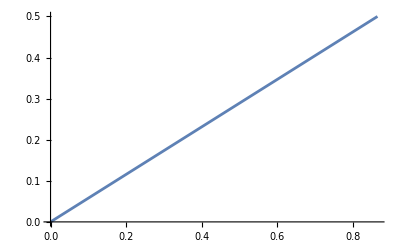

```mathematica
ListLinePlot[{{0,0},R1.V1}]
```

```mathematica
Clear[{alpha, beta}]
R2 = {{Cos[alpha], -Sin[alpha]},{Sin[alpha], Cos[alpha]}}
```

{{Cos[alpha],-Sin[alpha]},{Sin[alpha],Cos[alpha]}}

```mathematica
alpha = 30 Degree
R3 = R2
```

30 °

{{(√3)/2,-1/2},{1/2,(√3)/2}}

```mathematica
alpha = 31 Degree
R4 = R2
```

31 °

{{Cos[31 °],-Sin[31 °]},{Sin[31 °],Cos[31 °]}}

```mathematica
alpha = 32 Degree
R5 = R2
```

32 °

{{Cos[32 °],-Sin[32 °]},{Sin[32 °],Cos[32 °]}}

```mathematica
N[{R5 - R4,R4 - R3}]
```

{{{-0.0091192,-0.0148812},{0.0148812,-0.0091192}},{{-0.0088581,-0.0150381},{0.0150381,-0.0088581}}}

```mathematica
TODO(zz) here.
result = {}
For[i = 1,i < 360,++i, Insert[result,{}]]
Length[result]
```

{}

0

```mathematica
For[i = 1, i < 360, ++i, 
Append[result,
{N[Cos[i] - Cos[i - 1]],1}
]
]
Length[result]
```

Append::normal: Nonatomic expression expected at position 1 in Append[result,{{-0.459698,1}}].

Append::normal: Nonatomic expression expected at position 1 in Append[result,{{-0.956449,1}}].

Append::normal: Nonatomic expression expected at position 1 in Append[result,{{-0.573846,1}}].

General::stop: Further output of Append::normal will be suppressed during this calculation.

0

### TODO